# BigData Optimal Tax: Life-Cycle

This notebook takes the basic life cycle model and examines what happens for many alternative combinations of capital and labor tax rates.

```mathematica
x=0; Remove["Global`*"];
```

```mathematica
Needs["IPOPTLink`"];
 T=60;Tret=45;
r=0.1;R=1 + r; 
β=.95;
u[c_,l_] =c^(1-γ)/(1-γ)-B l^(1+η)/(1+η);
(* Specify age-wage path*)
Do[w[t]=-36.9994+3.52022(t+17)-.101878(t+17)^2+.00134816(t+17)^3-7.06233*10^-6(t+17)^4,{t,1,Tret}];
wagelist=Table[If[i≤ Tret,w[i],0],{i,T}];
Tax[capInc_,labInc_]=τK (R-1) capInc   +τL labInc;
PVrevL= Sum[τL w[t] l[t] R^(-t+1),{t,1,Tret}] ;
PVrevK= Sum[τK (R-1) a[t] R^(-t+1),{t,1,T}] ;
PVrevC= Sum[τC c[t] R^(-t+1),{t,1,T}] ;
obj = Sum[β^(t-1) u[c[t],l[t]],{t,1,T}];
(*Define Budget Constraints*)
bc1=Table[(R  a[t]+w[t] l[t]-c[t]-Tax[ a[t],w[t] l[t]])-a[t+1]≥ 0,{t,1,T}];
(*Define bound Constraints*)
bcaT={a[T+1]≥ 0};
abnds=Table[a[t]≥ amin,{t,2,T}];
lbndsc=Table[c[t]≥ 0.0001,{t,1,T}];
lbndsl=Map[#≥0&,Table[l[t],{t,1,Tret}]]; 
{vars,varbounds} = (Union[abnds,bcaT,lbndsc,lbndsl ]/.{( a_≥ b_  ) -> {a,b,∞}}//Transpose)/. {v_,lb_,ub_}:> {v,Transpose[{lb,ub}]};

ipoptConstraintStyle= 
{
	( a_== b_  ) -> LessEqual[0,a-b,0],
	( a_ <=  b_ ) -> LessEqual[-∞,a-b,0],
	(a_ >= b_  ) -> LessEqual[0,a-b,∞]
};
{budgetconstraintfunctions,budgetconstraintvals} = Transpose[bc1 /.ipoptConstraintStyle/. LessEqual[lb_,v_,ub_]-> {v,{lb,ub}} ];
(*Set initial guess for all variables to be 1; probably not a feasible point but better than letting them be zero.*)
varsinit=Table[1,Length[vars]];
(*Define border conditions particular to the problem*)
a[1]=0;
Do[ l[i]=0,{i,Tret+1,T}];
pfunc := ParametricIPOPTMinimize[-obj,
						vars,
						Table[start[i],{i,1,Length[vars]}],
						varbounds,
						budgetconstraintfunctions,
						budgetconstraintvals,
						Join[Table[start[i],{i,1,Length[vars]}],{τK,τL,amin,γ,η,B}]];
f[initialguess_List,params_List]:=
Block[{a,c,l,utility,PVrevK0,PVrevL0,τK0,τL0,amin0,γ0,η0,B0},
τK0=params[[1]];
τL0=params[[2]];
amin0=params[[3]];
γ0=params[[4]];
η0=params[[5]];
B0=params[[6]];
ipoptOut = pfunc[Sequence@@Join[initialguess,{τK0,τL0,amin0,γ0,η0,B0}]];
sol = IPOPTArgMin[ipoptOut];
utility = -IPOPTMinValue[ipoptOut];
Sow[{utility,sol,τK0,τL0}];
sol
];
gamlist={1/2};
etalist={1};
tkmax=0.4; tlmax=0.4;
dtk=0.05; dtl=0.05;
ntk=tkmax/dtk+1;
ntl=tlmax/dtl + 1;
possibilities = Flatten[Table[{tk,tl,aamin,gam,eeta,n},{tk,0,tkmax,dtk},{tl,0,tlmax,dtl},{aamin,{0}},{gam,gamlist},{eeta,etalist},{n,{1}}],5];
snake= Flatten[MapThread[If[#2==1,Reverse[#1],#1]&,{Partition[possibilities,Round[ntk]],1-Mod[Range[Round[ntk]],2]}],1];
jobs = Partition[snake,UpTo[Ceiling[Length[snake]/$ProcessorCount]]];
```

```mathematica
(*(*n=5;k=4
lst=Range[n]
b=Mod[n,k]
a=k-b
s=Quotient[n,k]
small=Take[Partition[lst,s],a
big=Partition[Drop[lst,a s],s+1]*)
BinBalanced[possibilities,$ProcessorCount]*)
sequentialSolve[parametervals_]:=
(pfunc := ParametricIPOPTMinimize[-obj,
							vars,
							Table[start[i],{i,1,Length[vars]}],
							varbounds,
							budgetconstraintfunctions,
							budgetconstraintvals,
							Join[Table[start[i],{i,1,Length[vars]}],{τK,τL,amin,γ,η,B}]];
(*Fold[f,varsinit,parametervals[[1;;2]]]*)
(*f[varsinit,parametervals[[1]]]*)
Reap[Fold[f,varsinit,parametervals]][[2]][[1]])
outputs = Flatten[ParallelMap[sequentialSolve,jobs],1]
(*jobs*)
```

NDSolve`ParametricPlugInFunction::dspar: -- Message text not found -- (0.)

General::stop: Further output of NDSolve`ParametricPlugInFunction::dspar will be suppressed during this calculation.

{1}
 |  |  |  |

```mathematica
isAsset[x_[_]] =x ==a;
SetAttributes[isAsset,Listable];
assetsloc = isAsset[vars];
isLabor[x_[_]] =x ==l;
SetAttributes[isLabor,Listable];
laborloc = isLabor[vars];
Rlist = Table[R^(-t+1),{t,1,T}];
nicetablefast[outputrow_List]:=Module[{utility,solvals,tK,tL },
utility = outputrow[[1]];
solvals=outputrow[[2]];
tK=outputrow[[3]];
tL =outputrow[[4]];
alist = Join[{0},Pick[solvals,assetsloc]];
llist = Pick[solvals,laborloc];
PVrevLmod = Total[tL wagelist[[1;;Tret]] llist Rlist[[1;;Tret]]];
PVrevKmod = Total[tK(R-1)alist [[1;;T]]Rlist[[1;;T]]];
totalPVrev = PVrevLmod + PVrevKmod;
{{{{{utility,totalPVrev,PVrevLmod,PVrevKmod,tK,tL}}}}}
]
data = Partition[ParallelMap[nicetablefast,outputs],Round[ntk]]
(*data = Flatten[MapThread[If[#2==1,Reverse[#1],#1]&,{data,1-Mod[Range[Round[ntk]],2]}],1];*)
(*]
data = lifecycle[60,45,0.1,0.95]*)
```

NDSolve`ParametricPlugInFunction::dspar: -- Message text not found -- (0.)

General::stop: Further output of NDSolve`ParametricPlugInFunction::dspar will be suppressed during this calculation.

Pick::incomp: Expressions IPOPTLink`IPOPTArgMin[NDSolve`ParametricPlugInFunction[IPOPTLink`ParametricIPOPTData[51,{«1»,«10»,«23»},{start[1],start[2],start[3],start[4],start[5],start[6],start[7],start[8],start[9],start[10],start[11],start[12],start[13],start[14],start[15],start[16],start[17],start[18],start[19],start[20],start[21],start[22],start[23],start[24],start[25],start[26],start[27],start[28],start[29],start[30],start[31],start[32],start[33],start[34],start[35],start[36],start[37],start[38],start[39],start[40],start[41],start[42],start[43],start[44],start[45],start[46],start[47],start[48],start[49],start[50],«121»}],«3»][«1»]] and {True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,«115»} have incompatible shapes.

Pick::incomp: Expressions IPOPTLink`IPOPTArgMin[NDSolve`ParametricPlugInFunction[IPOPTLink`ParametricIPOPTData[53,{«1»,«10»,«23»},{start[1],start[2],start[3],start[4],start[5],start[6],start[7],start[8],start[9],start[10],start[11],start[12],start[13],start[14],start[15],start[16],start[17],start[18],start[19],start[20],start[21],start[22],start[23],start[24],start[25],start[26],start[27],start[28],start[29],start[30],start[31],start[32],start[33],start[34],start[35],start[36],start[37],start[38],start[39],start[40],start[41],start[42],start[43],start[44],start[45],start[46],start[47],start[48],start[49],start[50],«121»}],«3»][«1»]] and {True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,«115»} have incompatible shapes.

Pick::incomp: Expressions IPOPTLink`IPOPTArgMin[NDSolve`ParametricPlugInFunction[IPOPTLink`ParametricIPOPTData[55,{«1»,«10»,«23»},{start[1],start[2],start[3],start[4],start[5],start[6],start[7],start[8],start[9],start[10],start[11],start[12],start[13],start[14],start[15],start[16],start[17],start[18],start[19],start[20],start[21],start[22],start[23],start[24],start[25],start[26],start[27],start[28],start[29],start[30],start[31],start[32],start[33],start[34],start[35],start[36],start[37],start[38],start[39],start[40],start[41],start[42],start[43],start[44],start[45],start[46],start[47],start[48],start[49],start[50],«121»}],«3»][«1»]] and {True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,«115»} have incompatible shapes.

Pick::incomp: Expressions IPOPTLink`IPOPTArgMin[NDSolve`ParametricPlugInFunction[IPOPTLink`ParametricIPOPTData[57,{«1»,«10»,«23»},{start[1],start[2],start[3],start[4],start[5],start[6],start[7],start[8],start[9],start[10],start[11],start[12],start[13],start[14],start[15],start[16],start[17],start[18],start[19],start[20],start[21],start[22],start[23],start[24],start[25],start[26],start[27],start[28],start[29],start[30],start[31],start[32],start[33],start[34],start[35],start[36],start[37],start[38],start[39],start[40],start[41],start[42],start[43],start[44],start[45],start[46],start[47],start[48],start[49],start[50],«121»}],«3»][«1»]] and {True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,«115»} have incompatible shapes.

Join::heads: Heads List and Pick at positions 1 and 2 are expected to be the same.

Pick::incomp: Expressions IPOPTLink`IPOPTArgMin[NDSolve`ParametricPlugInFunction[IPOPTLink`ParametricIPOPTData[51,{«1»,«10»,«23»},{start[1],start[2],start[3],start[4],start[5],start[6],start[7],start[8],start[9],start[10],start[11],start[12],start[13],start[14],start[15],start[16],start[17],start[18],start[19],start[20],start[21],start[22],start[23],start[24],start[25],start[26],start[27],start[28],start[29],start[30],start[31],start[32],start[33],start[34],start[35],start[36],start[37],start[38],start[39],start[40],start[41],start[42],start[43],start[44],start[45],start[46],start[47],start[48],start[49],start[50],«121»}],«3»][«1»]] and {a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,«115»} have incompatible shapes.

Pick::incomp: Expressions IPOPTLink`IPOPTArgMin[NDSolve`ParametricPlugInFunction[IPOPTLink`ParametricIPOPTData[53,{«1»,«10»,«23»},{start[1],start[2],start[3],start[4],start[5],start[6],start[7],start[8],start[9],start[10],start[11],start[12],start[13],start[14],start[15],start[16],start[17],start[18],start[19],start[20],start[21],start[22],start[23],start[24],start[25],start[26],start[27],start[28],start[29],start[30],start[31],start[32],start[33],start[34],start[35],start[36],start[37],start[38],start[39],start[40],start[41],start[42],start[43],start[44],start[45],start[46],start[47],start[48],start[49],start[50],«121»}],«3»][«1»]] and {a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,«115»} have incompatible shapes.

Pick::incomp: Expressions IPOPTLink`IPOPTArgMin[NDSolve`ParametricPlugInFunction[IPOPTLink`ParametricIPOPTData[55,{«1»,«10»,«23»},{start[1],start[2],start[3],start[4],start[5],start[6],start[7],start[8],start[9],start[10],start[11],start[12],start[13],start[14],start[15],start[16],start[17],start[18],start[19],start[20],start[21],start[22],start[23],start[24],start[25],start[26],start[27],start[28],start[29],start[30],start[31],start[32],start[33],start[34],start[35],start[36],start[37],start[38],start[39],start[40],start[41],start[42],start[43],start[44],start[45],start[46],start[47],start[48],start[49],start[50],«121»}],«3»][«1»]] and {a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,«115»} have incompatible shapes.

Pick::incomp: Expressions IPOPTLink`IPOPTArgMin[NDSolve`ParametricPlugInFunction[IPOPTLink`ParametricIPOPTData[57,{«1»,«10»,«23»},{start[1],start[2],start[3],start[4],start[5],start[6],start[7],start[8],start[9],start[10],start[11],start[12],start[13],start[14],start[15],start[16],start[17],start[18],start[19],start[20],start[21],start[22],start[23],start[24],start[25],start[26],start[27],start[28],start[29],start[30],start[31],start[32],start[33],start[34],start[35],start[36],start[37],start[38],start[39],start[40],start[41],start[42],start[43],start[44],start[45],start[46],start[47],start[48],start[49],start[50],«121»}],«3»][«1»]] and {a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,«115»} have incompatible shapes.

Pick::incomp: Expressions IPOPTLink`IPOPTArgMin[NDSolve`ParametricPlugInFunction[IPOPTLink`ParametricIPOPTData[51,{«1»,«10»,«23»},{start[1],start[2],start[3],start[4],start[5],start[6],start[7],start[8],start[9],start[10],start[11],start[12],start[13],start[14],start[15],start[16],start[17],start[18],start[19],start[20],start[21],start[22],start[23],start[24],start[25],start[26],start[27],start[28],start[29],start[30],start[31],start[32],start[33],start[34],start[35],start[36],start[37],start[38],start[39],start[40],start[41],start[42],start[43],start[44],start[45],start[46],start[47],start[48],start[49],start[50],«121»}],«3»][«1»]] and {a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,«115»} have incompatible shapes.

Pick::incomp: Expressions IPOPTLink`IPOPTArgMin[NDSolve`ParametricPlugInFunction[IPOPTLink`ParametricIPOPTData[53,{«1»,«10»,«23»},{start[1],start[2],start[3],start[4],start[5],start[6],start[7],start[8],start[9],start[10],start[11],start[12],start[13],start[14],start[15],start[16],start[17],start[18],start[19],start[20],start[21],start[22],start[23],start[24],start[25],start[26],start[27],start[28],start[29],start[30],start[31],start[32],start[33],start[34],start[35],start[36],start[37],start[38],start[39],start[40],start[41],start[42],start[43],start[44],start[45],start[46],start[47],start[48],start[49],start[50],«121»}],«3»][«1»]] and {a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,«115»} have incompatible shapes.

Pick::incomp: Expressions IPOPTLink`IPOPTArgMin[NDSolve`ParametricPlugInFunction[IPOPTLink`ParametricIPOPTData[55,{«1»,«10»,«23»},{start[1],start[2],start[3],start[4],start[5],start[6],start[7],start[8],start[9],start[10],start[11],start[12],start[13],start[14],start[15],start[16],start[17],start[18],start[19],start[20],start[21],start[22],start[23],start[24],start[25],start[26],start[27],start[28],start[29],start[30],start[31],start[32],start[33],start[34],start[35],start[36],start[37],start[38],start[39],start[40],start[41],start[42],start[43],start[44],start[45],start[46],start[47],start[48],start[49],start[50],«121»}],«3»][«1»]] and {a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,«115»} have incompatible shapes.

Pick::incomp: Expressions IPOPTLink`IPOPTArgMin[NDSolve`ParametricPlugInFunction[IPOPTLink`ParametricIPOPTData[57,{«1»,«10»,«23»},{start[1],start[2],start[3],start[4],start[5],start[6],start[7],start[8],start[9],start[10],start[11],start[12],start[13],start[14],start[15],start[16],start[17],start[18],start[19],start[20],start[21],start[22],start[23],start[24],start[25],start[26],start[27],start[28],start[29],start[30],start[31],start[32],start[33],start[34],start[35],start[36],start[37],start[38],start[39],start[40],start[41],start[42],start[43],start[44],start[45],start[46],start[47],start[48],start[49],start[50],«121»}],«3»][«1»]] and {a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,«115»} have incompatible shapes.

General::stop: Further output of Pick::incomp will be suppressed during this calculation.

Part::take: Cannot take positions 1 through 60 in Join[{0},Pick[IPOPTLink`IPOPTArgMin[NDSolve`ParametricPlugInFunction[«1»][1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,«121»]],{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,«115»}]].

Join::heads: Heads List and Pick at positions 1 and 2 are expected to be the same.

Part::take: Cannot take positions 1 through 60 in Join[{0},Pick[IPOPTLink`IPOPTArgMin[NDSolve`ParametricPlugInFunction[«1»][1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,«121»]],{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,«115»}]].

Join::heads: Heads List and Pick at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

Part::take: Cannot take positions 1 through 60 in Join[{0},Pick[IPOPTLink`IPOPTArgMin[NDSolve`ParametricPlugInFunction[«1»][1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,«121»]],{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,«115»}]].

General::stop: Further output of Part::take will be suppressed during this calculation.

NDSolve`ParametricPlugInFunction::dspar: -- Message text not found -- (0.)

$Aborted[]

General::stop: Further output of NDSolve`ParametricPlugInFunction::dspar will be suppressed during this calculation.

Pick::incomp: Expressions IPOPTArgMin[NDSolve`ParametricPlugInFunction[«1»][1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,«121»]] and {True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,«115»} have incompatible shapes.

Join::heads: Heads List and Pick at positions 1 and 2 are expected to be the same.

Part::take: Cannot take positions 1 through 60 in Join[{0},Pick[IPOPTArgMin[«1»],{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,«115»}]].

Pick::incomp: Expressions IPOPTArgMin[NDSolve`ParametricPlugInFunction[«1»][1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,«121»]] and {a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,a==l,«115»} have incompatible shapes.

General::stop: Further output of Pick::incomp will be suppressed during this calculation.

Join::heads: Heads List and Pick at positions 1 and 2 are expected to be the same.

Part::take: Cannot take positions 1 through 60 in Join[{0},Pick[IPOPTArgMin[«1»],{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,«115»}]].

Join::heads: Heads List and Pick at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

Part::take: Cannot take positions 1 through 60 in Join[{0},Pick[IPOPTArgMin[«1»],{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,«115»}]].

General::stop: Further output of Part::take will be suppressed during this calculation.

{}

output data

```mathematica
data>> dataoutMay2;
```

Next, we read the file

```mathematica
Clear[data]
data=<<dataoutMay2;
```

## The Pareto frontier - tables

In this notebook we care about utility versus revenue. I look forward to higher-dimensional frontiers.

Define Pareto function and Pareto frontier

Function h receives:
	Data in from database of cases
	Target revenue
	Indices - γind and ηind - indicating preference parameters

Function h outputs the optimal element for that revenue, and the policies that produced that outcome.

```mathematica
h[data_,revenue_, alimind_,γind_,ηind_]:=Module[
{dataflat,util,comb},
dataflat=Flatten[data[[All,All,alimind,γind,ηind,1]],1];
util=Max[Select[dataflat,#[[2]]≥revenue&][[All,1]]];
comb=Select[dataflat,#[[1]]==util&]
]
```

```mathematica
casesprefs=Table[{gamlist[[gam]],etalist[[eeta]]},{gam,1,Length[gamlist]},{eeta,1,Length[gamlist]}];
casesprefs=Flatten[casesprefs,1];
```

```mathematica
cases=Table[{1,gam,eeta},{gam,1,Length[gamlist]},{eeta,1,Length[gamlist]}];
cases=Flatten[cases,1];
```

```mathematica
numcases=Length[cases];
count=0;
```

```mathematica
outcmd:= (count=count+1;
{i,j,k}=cases[[count]];
Print["gamma = ",casesprefs[[count]][[1]],",   eta = ",casesprefs[[count]][[2]]]
maxrev=Transpose[Flatten[data[[All,All,i,j,k,1]],1]][[2]]//Max;
tb=Table[h[data,rev,i,j,k][[1]],{rev,0,0.99 maxrev ,0.04 maxrev}];
TableForm[tb,TableHeadings->{{},{"util","revtot","revk","revl","tk","tl"}}])
```

```mathematica
outcmdold:= (
count=count+1;
{i,j,k}=cases[[count]];
Print["gamma = ",casesprefs[[count]][[1]],",   eta = ",casesprefs[[count]][[2]]]
maxrev=Transpose[Flatten[data[[All,All,i,j,k,1]],1]][[2]]//Max;
Table[h[data,rev,i,j,k][[1]],{rev,0,0.96 maxrev ,0.02 maxrev}]//TableForm)
```

```mathematica
outcmd
```

gamma = 1/2,   eta = 1

| util | revtot | revk | revl | tk | tl
 | 116.907 | 0. | 0. | 0. | 0. | 0.
 | 112.977 | 6.1758 | 6.1758 | 0. | 0. | 0.05
 | 112.977 | 6.1758 | 6.1758 | 0. | 0. | 0.05
 | 112.977 | 6.1758 | 6.1758 | 0. | 0. | 0.05
 | 108.977 | 12.131 | 12.131 | 0. | 0. | 0.1
 | 108.977 | 12.131 | 12.131 | 0. | 0. | 0.1
 | 108.977 | 12.131 | 12.131 | 0. | 0. | 0.1
 | 104.903 | 17.8531 | 17.8531 | 0. | 0. | 0.15
 | 104.903 | 17.8531 | 17.8531 | 0. | 0. | 0.15
 | 104.903 | 17.8531 | 17.8531 | 0. | 0. | 0.15
 | 100.747 | 23.3279 | 23.3279 | 0. | 0. | 0.2
 | 100.747 | 23.3279 | 23.3279 | 0. | 0. | 0.2
 | 100.747 | 23.3279 | 23.3279 | 0. | 0. | 0.2
 | 96.6525 | 26.3695 | 17.0892 | 9.28027 | 0.1 | 0.15
 | 96.6525 | 26.3695 | 17.0892 | 9.28027 | 0.1 | 0.15
 | 96.5047 | 28.5393 | 28.5393 | 0. | 0. | 0.25
 | 92.8241 | 30.8894 | 22.3298 | 8.55963 | 0.1 | 0.2
 | 92.4028 | 32.7665 | 27.9044 | 4.86217 | 0.05 | 0.25
 | 88.9149 | 35.172 | 27.3182 | 7.85387 | 0.1 | 0.25
 | 88.249 | 37.1588 | 32.7239 | 4.43486 | 0.05 | 0.3
 | 87.7236 | 38.0938 | 38.0938 | 0. | 0. | 0.35
 | 83.9949 | 41.264 | 37.2464 | 4.0176 | 0.05 | 0.35
 | 83.9949 | 41.264 | 37.2464 | 4.0176 | 0.05 | 0.35
 | 79.6303 | 45.0575 | 41.4466 | 3.61091 | 0.05 | 0.4
 | 79.6303 | 45.0575 | 41.4466 | 3.61091 | 0.05 | 0.4

## The Pareto frontier - graphs

### Plot all data

We plot all the data points in revenue-utility space. This helps us see where the good points are. I also use colors to indicate the policies.

plot

```mathematica
tmax=Max[tkmax,tlmax]
```

0.4

```mathematica
plot[alimind_,γind_,ηind_]:=Module[

{alimi=alimind,γi=γind,ηi=ηind,Βi=1,dots,colorF,gra1,gra2,plotLegend,leg},

dots=Flatten[data[[All,All,alimi,γi,ηi,Βi]],1];

colorF=Blend[{{0,Green},{tmax,Red}},#]&;

gra1=Graphics[
{{colorF[#5],Tooltip[Point[{#2,#1}],{#5,#6}]}&@@@dots,Text["τK",{Max[dots[[All,2]]]/2,Max[dots[[1,1]]]},{0,-1}]},
Frame->{{True,False},{True,False}}, 
PlotRange->All,
AxesOrigin->{0,0},
FrameLabel-> {"Total Tax Revenue","Consumer Utility"},
ImageSize->Medium,
AxesOrigin-> {0,0}];

gra2=Graphics[{{colorF[#6],Tooltip[Point[{#2,#1}],{#5,#6}]}&@@@dots,Text["τL",{Max[dots[[All,2]]]/2,Max[dots[[1,1]]]},{0,-1}]},Frame->{{True,False},{True,False}}, PlotRange->All,AxesOrigin->{0,0},FrameLabel->{"Total Tax Revenue","Consumer Utility"},ImageSize->Medium,AxesOrigin-> {0,0}];

plotLegend[{min_,max_},n_,col_]:=Graphics[MapIndexed[{{col[#1],Rectangle[{0,#2[[1]]-1},{1,#2[[1]]}]},{Black,Text[NumberForm[N@#1,{4,2}],{4,#2[[1]]-.5},{1,0}]}}&,Rescale[Range[n],{1,n},{min,max}]],Frame->True,FrameTicks->None,PlotRangePadding->.5];

leg=plotLegend[{0,0.8},20,colorF];
Grid[{{Row[{"γ= ",2^(γi-2), ", η= ",Piecewise[{{10,ηi==4},{5,ηi==3}},ηi ] , ", Borrowinglimit= ",Piecewise[{{-(alimi-1)*10,alimi<4},{-50,alimi==4}},-∞]}],SpanFromLeft},{gra1,gra2,leg}},ItemSize->Automatic]
]
```

```mathematica
count=0;
```

```mathematica
prntcmd:=(
count=count+1;
{i,j,k}=cases[[count]];
Print["gamma = ",casesprefs[[count]][[1]],",   eta = ",casesprefs[[count]][[2]]];
plot[i,j,k])
```

Each plot is a point in utility-revenue space. The left one uses color to indicate the size of the capital income tax; the right one does so for the labor income tax.
Note that there are some red points in the τL graph that are on the frontier, but the red points in the τK graph are all inferior.

gamma = 1/2,   eta = 1

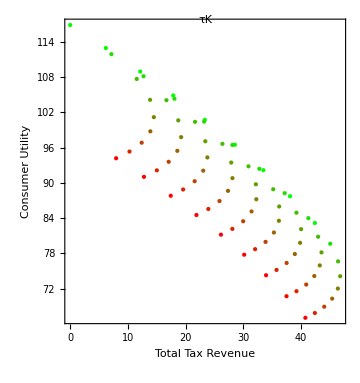
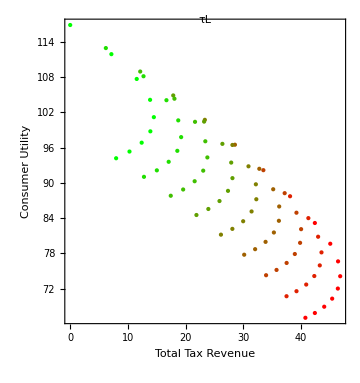
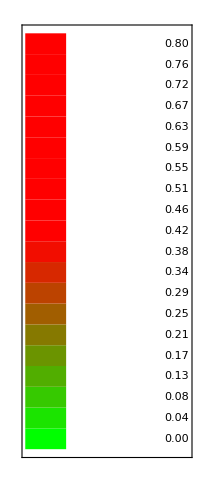
γ= 1/2, η= 1, Borrowinglimit= 0 |  | 
-Graphics- | -Graphics- | -Graphics-

```mathematica
prntcmd
```

```mathematica
time
```

time